```mathematica
lemniscate=ParametricPlot[{Sin[t]/(1+Cos[t]^2),Sin[t] Cos[t]/(1+Cos[t]^2)},{t,0,2 Pi},PlotStyle->Black][[1]];
```

```mathematica
circle=Graphics[{Blue,Thick,Circle[{0,0},1.5]}][[1]];
```

```mathematica
triangle=Graphics[RegularPolygon[3]][[1]];
```

```mathematica
pentagon=Graphics[RegularPolygon[5]][[1]];
```

```mathematica
line=Graphics[{Red,Thick,Line[{{-1,0},{1,0}}]}][[1]];
```

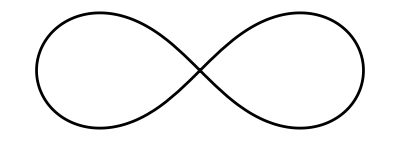
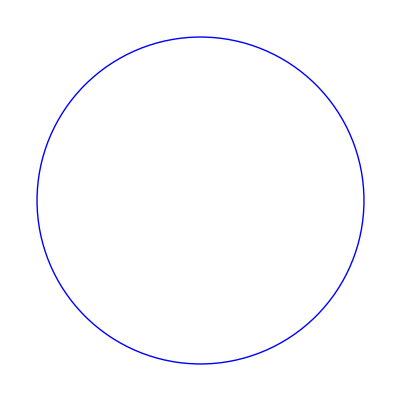

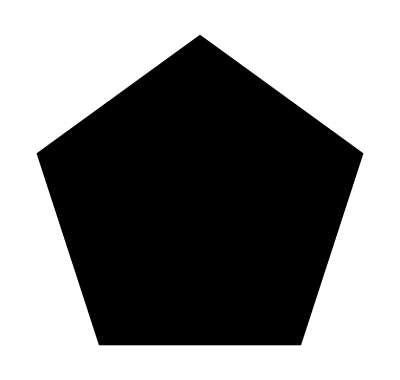
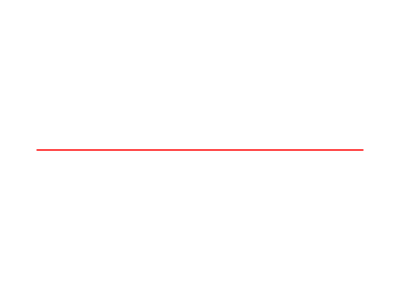

```mathematica
{Graphics[lemniscate],Graphics[circle],Graphics[triangle],Graphics[pentagon],Graphics[line]} (* Show *)
```

```mathematica
transformationF[obj_,a_,center_] :=GeometricTransformation[obj,RotationTransform[a,center]]
```

```mathematica
myMenu=PopupMenu[Dynamic[object],{lemniscate->"Lemniscate",circle->"Circle",triangle->"Triangle",pentagon->"Pentagon",line->"Line"}]
```

```mathematica
Dynamic[mode]
```

```mathematica
mode = {{3,0}->"{3,0}",{0,0}->"origin"}
```

{{3,0}→{3,0},{0,0}→origin}

```mathematica
{Manipulate[Graphics[transformationF[object,a,center],PlotRange->7,Axes->True],{a,0,2*Pi},{center,mode}],myMenu}
```

{,}